```mathematica
L1[x_] = (x*(x-0.2)*(x-0.3))/ (0.1 * (0.1 - 0.2) * (0.1- 0.3))
```

500. (-0.3+x) (-0.2+x) x

```mathematica
L2[x_] = (x*(x-0.1)*(x-0.3))/ (0.2 * (0.2 - 0.1) * (0.2- 0.3))
```

-500. (-0.3+x) (-0.1+x) x

```mathematica
L3[x_] = (x*(x-0.1)*(x-0.2))/ (0.3 * (0.3 - 0.1) * (0.3- 0.2))
```

166.667 (-0.2+x) (-0.1+x) x

```mathematica
L[x_] = (E^0.1)*L1[x] + (E^0.2)*L2[x] + (E^0.3)*L3[x] // Simplify
```

x (19.3336-99.5051 x+166.861 x^2)

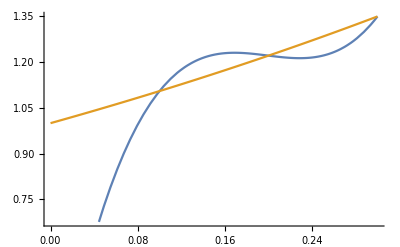

```mathematica
Plot[{Simplify[L[x]], E^x}, {x, 0, 0.3}]
```

```mathematica
R[x_] = E^x - L[x] // Simplify
```

ⅇ^x+x (-19.3336+99.5051 x-166.861 x^2)

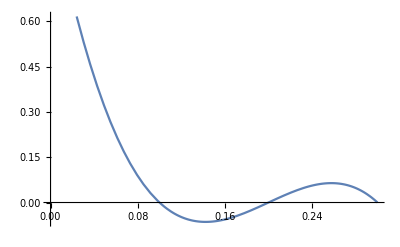

```mathematica
Plot[R[x], {x, 0,0.3}]
```

```mathematica
MaxR[x_] =(E^0.3)*Abs[x(x-0.1)(x-0.2)(x-0.3)]/24
```

0.0562441 Abs[(-0.3+x) (-0.2+x) (-0.1+x) x]

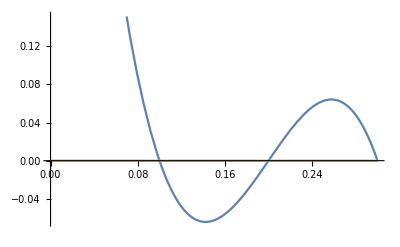

```mathematica
Plot[{R[x], MaxR[x]}, {x, 0, 0.3}]
```